# Rooftop Recognition for Solar Energy Potential

Last modified on: Sunday, July 8, 2018 at 17:15

The aim of this project is to detect the rooftop of buildings to determine the available area at different locations and to identify the most suitable ones for solar energy application such as solar PV using Neural Networks and satellite imagery.

## The Dataset

The Inria Aerial Image Labeling addresses a core topic in remote sensing: the automatic pixelwise labeling of aerial imagery (link to paper). Dataset features:

Coverage of 810 km.b2 (405 km.b2 for training and 405 km.b2 for testing)

Aerial orthorectified color imagery with a spatial resolution of 0.3 m

Ground truth data for two semantic classes : building and not building (publicly disclosed only for the training subset)

https : // project.inria.fr/aerialimagelabeling/

Import

Set the working directory:

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/enricocastro/Documents/GitHub/Project

Select the images for the input and those for the results:

```mathematica
trainFilesInput=Select[FileNames["image/*.tif"],!StringMatchQ[#,___~~"._"~~___]&];
trainFilesResult=StringReplace[#,"image/"->"mask/"]&/@trainFilesInput;
```

Import an image to test:

```mathematica
imgInput=Import[trainFilesInput⟦1⟧];
imgResult=Import[trainFilesResult⟦1⟧];
```

Partition of the images in 100 from a 5000x5000 to images 500x500 :

```mathematica
splicesInput=Join@@ImagePartition[imgInput,500];
splicesResults=Join@@ImagePartition[imgResult,500];
```

Check the size of the file:

```mathematica
Round[ImageData[splicesResults⟦10⟧]] // ByteCount
```

2000152

Due to the Join we have a list of 100 files that contain the 10x10 images that compose the original:

```mathematica
Length[splicesInput]
```

100

## Assemble Images

Assemble images in sets of ten to verify:

```mathematica
assambleImage=ImageAssemble[splicesInput⟦41;;50⟧]
```

-Graphics-

Assemble mask images in sets of ten to verify:

```mathematica
assambleMask=ImageAssemble[Image/@Round[ImageData/@splicesResults⟦41;;50⟧]]
```

-Graphics-

## Compose

Compose the images to verify image matching:

```mathematica
ImageCompose[assambleImage,{assambleMask,0.5}]
```

-Graphics-

```mathematica
rand=RandomInteger[{1,100}];
ImageCompose[splicesInput⟦rand⟧,{splicesResults⟦rand⟧,0.5}]
```

-Graphics-

## Association

```mathematica
mxTrain=Thread[splicesInput-> splicesResults];
```

```mathematica
ImageCompose[Keys[mxTrain⟦rand⟧],{Values[mxTrain⟦rand⟧],0.4}]
```

-Graphics-

#### Export test

First try to export the MX file:

```mathematica
Export["File.mx",mxTrain]
```

File.mx

Export

## mxFileCreator

The first approach to organize the data was to make MX files, one per image, each file contain the 100 images with their respective mask. In order to do that a function mxFileCreator was build.

Function that creates a MX file per each 5000x5000 image:

```mathematica
mxFileCreator[trainFilesInput_,trainFilesResult_,i_]:=Block[
	{Flag,imgInput,imgResult,splicesInput,splicesResults,mxTrain},

	Flag=TextString[i];

	imgInput=Import[trainFilesInput];
	imgResult=Import[trainFilesResult];

	splicesInput=Join@@ImagePartition[imgInput,500];
	splicesResults=Round[ImageData/@(Join@@ImagePartition[imgResult,500])];

	mxTrain=Thread[splicesInput-> splicesResults];

	Export["MXFiles/File"<>Flag<>".mx",mxTrain]
]
```

Test the function

```mathematica
mxFileCreator[trainFilesInput⟦1⟧,trainFilesResult⟦1⟧,1]
```

MXFiles/File1.mx

```mathematica
file=Import["MXFiles/File1.mx"];
file⟦RandomInteger[{1,100}]⟧
```

-Graphics-→{1}
 |  |  |  |

```mathematica
ImageCompose[Keys[file⟦rand⟧],{Image[Values[file⟦rand⟧]],0.5}]
```

-Graphics-

To Map all the images and convert them into association in a MX files :

```mathematica
MapIndexed[mxFileCreator[#[[1]], #[[2]], Echo[#2[[1]]]] &, Transpose[{trainFilesInput, trainFilesResult}]]
```

1

{MXFiles/File1.mx}

## Importing the created files

Import one random set of data for verification porpoises:

Import the MX file created:

```mathematica
fileImported=Import@FileNames["MXFiles/*.mx"]⟦1⟧;
```

Test the image association

```mathematica
ImageCompose[Keys[fileImported]⟦rand⟧,{Values[fileImported]⟦rand⟧//Image,0.5}]
```

-Graphics-

## The net

Net selection

The net selected for this project was at Wolfram Neural Net Repository for Semantic Segmentation. Released in 2016 by the University of Adelaide, Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data was modify to identify two classes instead of 21.

Take the net model for Semantic Segmentation from the repositories:

```mathematica
netModel=NetModel["Ademxapp Model A1 Trained on PASCAL VOC2012 and MS-COCO Data"]
```

NetChain[<>]

## Net surgery

### Modify the Input for the size of the images

Replace the encoder to accept images 500x500:

```mathematica
netModel500=NetReplacePart[netModel,"Input"->NetEncoder[{"Image",{500,500},"MeanImage"-> {0.485,0.456,0.406}}] ]
```

NetChain[<>]

### Resize the layer

Drop the last three layer to modify the net:

```mathematica
firstPartNet=NetDrop[netModel500,-3]
```

NetChain[<>]

### Convolution layer

Add a convolution layer to have two outputs:

```mathematica
convLayer=NetChain[{firstPartNet,ConvolutionLayer[2,{3,3},"Stride"-> {1,1},"PaddingSize"-> {12,12},"Dilation"-> {12,12}],ResizeLayer[{500,500}]}];
```

Take the last two layers from the one with the new encoder:

```mathematica
lastPartNet=NetReplacePart[NetTake[netModel500,-2],"Input"->Automatic]
```

NetChain[<>]

### SoftmaxLayer

Append the last layers and Softmax Layer with a net decoder of classes:

```mathematica
finalNet=NetAppend[convLayer,{lastPartNet⟦1⟧,SoftmaxLayer[]},"Output"->NetDecoder[{"Class",{0,1},"InputDepth"->3}]]
```

NetChain[<>]

### Initialize the net

Initialize the final net to check for errors:

```mathematica
iniFinalNet=NetInitialize[finalNet]
```

NetChain[<>]

Test the encoders and decoders of the initialize net:

```mathematica
Image[iniFinalNet[Keys[fileImported]⟦rand⟧],ImageSize->Small]
```

## Net to train

### Loss Function

Connect the final net to a loss function:

```mathematica
LossNet=NetGraph[<|"eval"->finalNet,"loss"->CrossEntropyLossLayer["Index"]|>,{"eval"->"loss"} ]
```

NetGraph[<>]

### Initialize and export the net to train

Initialize the LossNet:

```mathematica
iniLossNet=NetInitialize[LossNet]
```

NetGraph[<>]

Export the complete net for training:

```mathematica
Export["iniLossNet.wlnet",iniLossNet]
```

iniLossNet.wlnet

#### Test the LossNet

Test the LossNet with two input forms:

```mathematica
iniLossNet[<|"Input"-> fileImported⟦2,1⟧,"Target"-> fileImported⟦2,2⟧|>]
```

0.623051

```mathematica
iniLossNet[fileImported⟦2⟧]
```

0.623051

## Generator function

Reduce Dataset Size

From the MX files created in section

Set the file path for the MX files:

```mathematica
path="MXFiles/";
mxFiles=FileNames[path<>"*.mx"];
RandomSample[mxFiles,1]⟦1⟧
```

MXFiles/File1.mx

## Binary Files

Binary files are a way to reduce of the size while importing the train set. Once the files are binarize the file size reduces and ones read in can be deserialize. At the same time TIF images were converted to JPG to remove unnecessary information while reducing size.

### Binary write

Binary write:

```mathematica
binaryWrite[file_,expr_]:=With[{bytes=BinaryWrite[file,BinarySerialize[expr]]},Close[file];
bytes]
```

### Import and Reexport Function

Function to convert TIF images to JPG and matrix to Binary:

```mathematica
importAndReExport[path_,folder_]:=Block[{imported,imgs,masks,hashes},
	imported=Import[path];
	imgs=imported[[All,1]];
	masks=imported[[All,2]];
	hashes=Hash/@imgs;
	
	Print[MapThread[Export[folder<>"/"<>ToString[#1]<>".jpg",#2]&,{hashes,imgs}];//AbsoluteTiming];
	Print[MapThread[binaryWrite[folder<>"/"<>ToString[#1]<>".bin",#2]&,{hashes,masks}];//AbsoluteTiming];
	
	Clear[imported,imgs,masks,hashes]
]
```

Take each MX file and create the correspondent JPG and BIN file :

```mathematica
Table[importAndReExport[mxFiles[[i]], "binFiles"], {i, 1, Length[mxFiles], 1}]
```

{11.7403,Null}

{0.526345,Null}

{Null}

### Binary Read

Read the binary file and Deserialize the file:

```mathematica
BinaryDeserialize[ReadByteArray["/Users/enricocastro/Documents/GitHub/Project/binFiles/74004748475675200.bin"]]//Dimensions
```

{500,500}

```mathematica
FileNames["/Users/enricocastro/Documents/GitHub/Project/binFiles/*.bin"]//Length
```

100

## Training Out of Core

Partitional Function

### Data from MX files

Take the name of the JPG and BIN files:

```mathematica
trainingDataSet={FileNames["/Users/enricocastro/Documents/GitHub/Project/binFiles/*.jpg"], FileNames["/Users/enricocastro/Documents/GitHub/Project/binFiles/*.bin"]};
```

Set the data to train:

```mathematica
imageDataSet=Table[File[trainingDataSet[[1,i]]],{i,10}];
imageDataSet//ByteCount
```

1640

```mathematica
maskDataSet=Table[ReadByteArray[trainingDataSet[[2,i]]],{i,10}];
maskDataSet//ByteCount
```

2501170

Associate the image with his respective mask and take a random sample:

```mathematica
data=RandomSample@Thread[imageDataSet->maskDataSet];
data⟦2⟧
```

File[/Users/enricocastro/Documents/GitHub/Project/binFiles/1704941998246832348.jpg]→ByteArray[…]

Generator

In order to train the net with a big amount of data a generator function was created. The generator function load a single batch of data from an external source to train each time. NetTrain[net, f, …] calls f at each training batch iteration, thus only keeping a single batch of training data in memory. The function can depend on the batch size, which can be set or set automatic by the computer, the absolute batch that is the number of batches load during the training and the round.

partGenerator associate and load a batch of size BatchSize into the net training. In order to do so it takes partitions of the whole dataset in batches of size BatchSize and load the element of this partition taking the module of the AbsoluteBatch. The function also adds one to the mask matrix to get the right values for the net:

```mathematica
partGenerator=Function[Block[{batch,dataSet,batchData},
	If[!ValueQ[partitionedData],partitionedData=Partition[Range[Length[data]],#BatchSize,#BatchSize,1]];
	Print[Association@Thread[Keys[#]->Values[#]]];
	batch=Mod[#AbsoluteBatch,Floor[Length@data/#BatchSize]];
	batchData=data⟦partitionedData[[Echo@(batch+1)]]⟧;
	
	Thread[Keys[batchData]->1+BinaryDeserialize/@Values[batchData]]
	(*<|"Input"->Keys[batchData],"Target"->BinaryDeserialize/@Values[batchData]|>*)
]
];
```

#### Test of partGenerator

```mathematica
Clear[partitionedData]
```

```mathematica
Animate[partGeneratorData=partGenerator[<|"BatchSize"->2,"Round"->0,"AbsoluteBatch"->i|>];
Keys[partGeneratorData],{i,1,10,1},SaveDefinitions->True,Initialization:>False]
```

```mathematica
partGeneratorData⟦1,2⟧//Flatten//DeleteDuplicates
```

{1,2}

## Train test

Before training for a lot of data is always good to try first with a small set.

Clear partitionedData for different batch sizes:

```mathematica
ClearAll[partitionedData];
```

Import the net to train:

```mathematica
iniLossNet=Import["/Volumes/ECG/ProjectWSS/iniLossNet.wlnet"]
```

Set the checkpoint directory:

```mathematica
checkpointDir="/Volumes/ECG/ProjectWSS/AerialImageDataset/checkpoint"
```

/Volumes/ECG/ProjectWSS/AerialImageDataset/checkpoint

Net training with partGenerator:

```mathematica
iniLossTrainNet=NetTrain[iniLossNet,{partGenerator,"RoundLength"->3},All,MaxTrainingRounds->3,TrainingProgressCheckpointing->{"Directory",checkpointDir}]
```

NetTrain::netmem2: Insufficient memory to evaluate the network: at least 3.21 gigabytes are required but only 2.33 gigabytes are available for TargetDevice -> CPU.

$Failed

Trained Net

Once trained one can look at the relevant information of the training process.

Import the trained net as an object:

```mathematica
finalTrainedNet=Import["/Volumes/ECG/ProjectWSS/AerialImageDataset/TrainedNets/model_3740226865.mx"]
```

NetTrainResultsObject[<>]

### Encoder & Decoder

Set the encoders and decoders for further tests.

Set the encoder for image size 500x500 and a MeanImage:

```mathematica
enc=NetEncoder[{"Image",{500,500},"MeanImage"-> {0.485,0.456,0.406}}];
```

Set the decoder for the classe which 0 means no rooftop and 1 means rooftop:

```mathematica
dec=NetDecoder[{"Class",{0,1},"InputDepth"->3}];
```

### Training information

Information by batch:

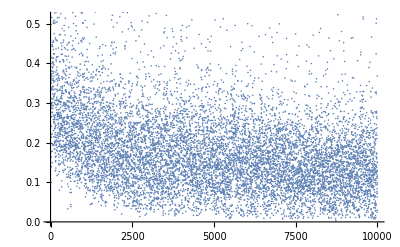
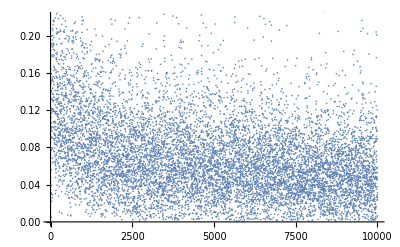

```mathematica
{ListPlot[finalTrainedNet["BatchLossList"]],ListPlot[finalTrainedNet["BatchErrorRateList"]]}
```

Information by round:

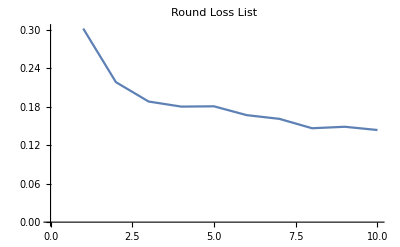
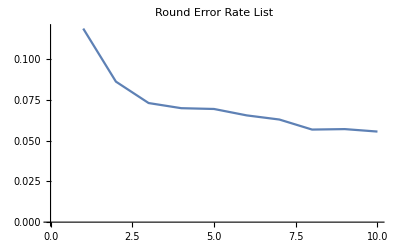

```mathematica
{ListLinePlot[finalTrainedNet["RoundLossList"],PlotLabel->"Round Loss List"],ListLinePlot[finalTrainedNet["RoundErrorRateList"],PlotLabel->"Round Error Rate List"]}
```

Information for the validation:

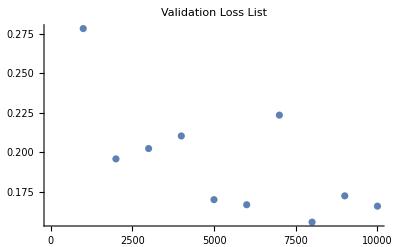
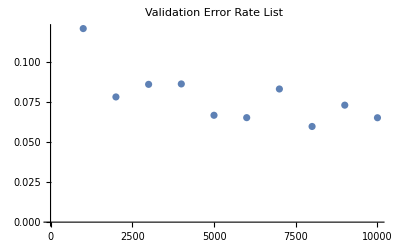

```mathematica
{ListPlot[finalTrainedNet["ValidationLossList"],PlotLabel->"Validation Loss List"],ListPlot[finalTrainedNet["ValidationErrorRateList"],PlotLabel->"Validation Error Rate List"]}
```

Loss evolution plot:

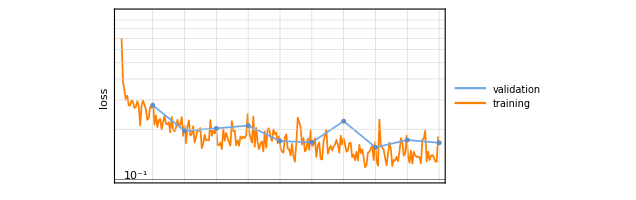

```mathematica
finalTrainedNet["LossEvolutionPlot"]
```

Error rate evolution plot:

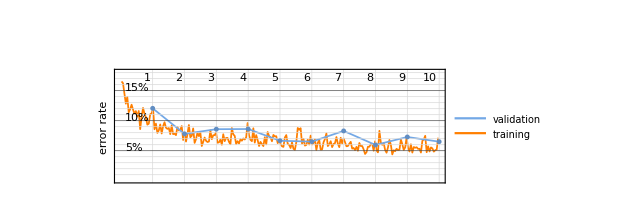

```mathematica
finalTrainedNet["ErrorRateEvolutionPlot"]
```

```mathematica
Transpose@{{Style["Properties",FontSize-> 18],"FinalRoundLoss","FinalRoundErrorRate","FinalValidationLoss","FinalValidationErrorRate","LowestValidationLoss","LowestValidationErrorRate","BatchSize","TotalRounds","TotalBatches","TotalInputs","TotalTrainingTime","MeanBatchesPerSecond","MeanInputsPerSecond","InitialLearningRate","FinalLearningRate","OptimizationMethod"},{Style["Values",FontSize-> 18],finalTrainedNet["FinalRoundLoss"],finalTrainedNet["FinalRoundErrorRate"],finalTrainedNet["FinalValidationLoss"],finalTrainedNet["FinalValidationErrorRate"],finalTrainedNet["LowestValidationLoss"],finalTrainedNet["LowestValidationErrorRate"],finalTrainedNet["BatchSize"],finalTrainedNet["TotalRounds"],finalTrainedNet["TotalBatches"],finalTrainedNet["TotalInputs"],UnitConvert[Quantity[finalTrainedNet["TotalTrainingTime"],"Seconds"],"Hours"],finalTrainedNet["MeanBatchesPerSecond"],finalTrainedNet["MeanInputsPerSecond"],finalTrainedNet["InitialLearningRate"],finalTrainedNet["FinalLearningRate"],finalTrainedNet["OptimizationMethod"]}}//Dataset
```

Dataset[<>]

Extract the trained net:

```mathematica
finalTrainedNetEval=NetExtract[finalTrainedNet["TrainedNet"],"eval"]
```

NetChain[<>]

Set the encoder:

```mathematica
finalTrainedNetEvalEnc=NetReplacePart[finalTrainedNetEval,"Input"->enc ]
```

NetChain[<>]

Set the decoder:

```mathematica
finalTrainedNetEvalDec=NetReplacePart[finalTrainedNetEvalEnc,"Output"->dec ]
```

NetChain[<>]

Export the net to test:

```mathematica
Export["/Volumes/ECG/ProjectWSS/AerialImageDataset/FinalTrainedNetEval.mx",finalTrainedNetEvalDec]
```

/Volumes/ECG/ProjectWSS/AerialImageDataset/FinalTrainedNetEval.mx

## Net Evaluation

```mathematica
netEvaluation=Import["/Volumes/ECG/ProjectWSS/AerialImageDataset/FinalTrainedNetEval.mx"]
```

NetChain[<>]

Files

Take a random file from the training set:

```mathematica
randomFile=RandomSample[FileNames["/Volumes/ECG/ProjectWSS/AerialImageDataset/train/images/*.tif"],1];
TestImage=Import[randomFile⟦1⟧];
TestMask=Import[StringReplace[randomFile⟦1⟧,"train/images/"->"train/gt/"]];
```

Take 100 partition of the image to feed into the net:

```mathematica
imageToTest=ImagePartition[TestImage,{500,500}];
maskToTest=ImagePartition[TestMask,{500,500}];
```

```mathematica
rand1=RandomInteger[{1,10}];
rand2=RandomInteger[{1,10}];
```

```mathematica
ImageCompose[imageToTest⟦rand1,rand2⟧,{Image[netEvaluation[imageToTest⟦rand1,rand2⟧]],0.5}]
```

```mathematica
ImageCompose[maskToTest⟦rand1,rand2⟧,{Image[netEvaluation[imageToTest⟦rand1,rand2⟧]],0.5}]
```

Compare the percentage of building in the area with the net and the mask:

```mathematica
{{"Net","Mask"},{ImageMeasurements[Image[finalTrainedNetEvalDec[imageToTest⟦rand1,rand2⟧]],"Mean"],ImageMeasurements[maskToTest⟦rand1,rand2⟧,"Mean"]}}//Dataset
```

Dataset[<>]

GeoImage

```mathematica
testImage[latitud_,longitud_,net_]:=Module[{geoImage,geoImageResize},
geoImage=GeoImage[GeoPosition[{latitud,longitud}],GeoRange->Quantity[75, "Meters"],GeoProjection->"Mercator",ImageSize->Small];
geoImageResize=ImageResize[geoImage,{500,500}];
{ImageCompose[geoImageResize,{Image[net[geoImageResize]],0.3}]
,Image[net[geoImageResize]]}]
```

```mathematica
GeoPosition[Entity["City",{"SanLuisPotosi","SanLuisPotosi","Mexico"}]]
```

GeoPosition[{22.16,-100.98}]

```mathematica
Manipulate[testImage[22.16+u,-100.98+u,finalTrainedNetEvalDec],{u,{-10,-10},{10,10}},ControlType->Slider2D,ControlPlacement->Left]
```

```mathematica
ImageMeasurements[Image[finalTrainedNetEvalDec[imageToTest⟦rand1,rand2⟧]],"Mean"]
```

0.138952

```mathematica
testImage[22.16+10,-100.98+10,finalTrainedNetEvalDec]
```

Image Matrix

```mathematica
ImageMeasurements[areaTest,"Mean"]
```

0.130916

## Google Images

```mathematica
GetSatImage[x_,y_,zoom_,range_]:=Image[GeoGraphics[GeoPosition[{x,y}],GeoServer->{"http://mt0.google.com/vt/lyrs=s&x=`2`&y=`3`&z=`1`"},GeoRange->Quantity[range,"Meters"],GeoZoomLevel->zoom]];
GetStreetImage[x_,y_,zoom_,range_]:=Image[GeoGraphics[GeoPosition[{x,y}],GeoBackground->GeoStyling["StreetMapNoLabels"],GeoRange->Quantity[range,"Meters"],GeoZoomLevel->zoom]];
```

```mathematica
Here
```

GeoPosition[{42.37,-71.24}]